(-Sin[0.700357 t] | Cos[0.700357 t] | 0
-Cos[0.700357 t] | -Sin[0.700357 t] | 20
0 | 0 | 1)

(0.4905 Sin[0.700357 t] | -0.4905 Cos[0.700357 t] | 0
0.4905 Cos[0.700357 t] | 0.4905 Sin[0.700357 t] | 0
0 | 0 | 0)

{1.,0.,1.}

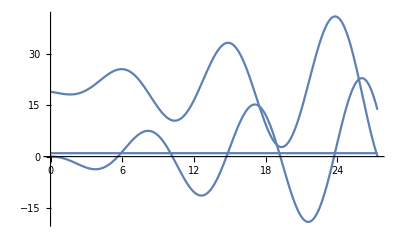

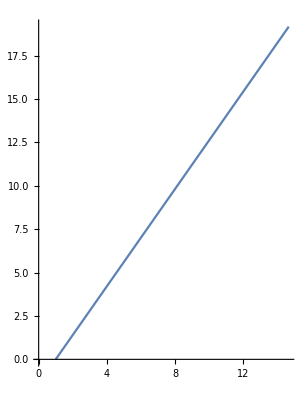

```mathematica
Clear[t]
r=20;
a = 9.81;
ω = Sqrt[a/r];
(*Clear[ω,r]*)
θ = ω*t;
RtoS[t_] := {
{-Sin[ω*t],-Cos[ω*t],r*Cos[ω*t]},
{Cos[ω*t],-Sin[ω*t],r*Sin[ω*t]},
{0,0,1}
};
ParametricPlot3D[{(RtoS[t]).{0,1,1},(RtoS[t]).{1,2,1}},{t,0,2}];
StoR[t_]:=Simplify[Inverse[RtoS[t]]];
StoR[t]//MatrixForm
StoR''[t]//MatrixForm
posRot = {0,19,1};
vRot = {0,-.5,0};
posAbs=RtoS[0].posRot
vAbs =RtoS'[0].posRot+RtoS[0].vRot;
pos[t_] := posAbs+t*vAbs;
relPos[t_]:=StoR[t].pos[t];

tMax = 27.361;

Plot[relPos[t],{t,0,tMax}]
plotSize = .01;
circle =Graphics[Circle[{0,r},r,{3Pi/2-plotSize/2,3Pi/2+plotSize/2}]];


SState[x_,v_,t_]:=RtoS[t].x


Manipulate[ParametricPlot[{relPos[t][[{1,2}]],SState[relPos[t],relPos'[t],t][[{1,2}]]},{t,0,tspan}],{tspan,0.001,tMax,0.01}]

ParametricPlot[SState[relPos[t],relPos'[t],t][[{1,2}]],{t,0.001,tMax}]
```